```mathematica
SetDirectory@NotebookDirectory[]
```

/home/eric/git/nonlinear-systems-lab/Project 1

```mathematica
rawdata=Import["data/raw/rocking1.tsv"]
```

{{time,1,2,3,4},{153.815,0,0,158.25,},{153.815,0,0,,601.5},{153.845,0,0,157.75,},{153.845,0,0,,600.75},{153.879,0,0,156.5,},1541,{177.536,0,0,,549.25},{177.58,0,0,105.75,},{177.58,0,0,,549.25},{177.609,0,0,105.75,},{177.609,0,0,,549.25}}
 |  |  |  |

```mathematica
tagDist=.396;
pivotFromTag =tagDist*0.26582;
pendulumlen = 0.335;
```

# Unify timestamps

```mathematica
preprocess[rawdata_]:=Module[{(*header,gathered,data,meandist, x,x1,x2,θ1,θ2*)},
header=ToString/@rawdata[[1]];
gathered=Gather[rawdata[[2;;All]],First[#1]==First[#2]&];
data=Transpose[Mean[Select[#,NumberQ]]&/@Transpose[#]&/@gathered];
meandist = Mean[Select[data[[5]]-data[[4]],NumberQ]];
(*Print[meandist];*)

(* Convert to meters *)
data[[2;;All]]= data[[2;;All]]*tagDist/meandist;

x=Mean[{data[[4]],data[[5]]-tagDist}];

x1=data[[3]]-(x+pivotFromTag);
x2=data[[2]]-(x+tagDist-pivotFromTag+.003);

θ1=ArcSin[x1/pendulumlen];
θ2=ArcSin[x2/pendulumlen];

Prepend[
Cases[
Transpose@{data[[1]],x,θ1,θ2},{_?NumberQ,_?NumberQ,_?NumberQ,_?NumberQ}],{"Time", "x", "theta1", "theta2"}]
]
```

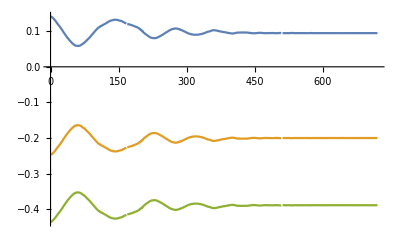

```mathematica
ListLinePlot[{x,x1,x2}]
```

```mathematica
data=preprocess[rawdata]
```

{{Time,x,theta1,theta2},{153.815,0.14123,-0.826853,-1.5708+0.754507 ⅈ},715,{177.609,0.0944585,-0.638745,-1.5708+0.556335 ⅈ}}
 |  |  |  |

```mathematica
ArcSin[{1,Mean[{}],1}]
```

{π/2,ArcSin[Mean[{}]],π/2}

```mathematica
Mean[θ2[[-100;;All]]]
```

0.000539319

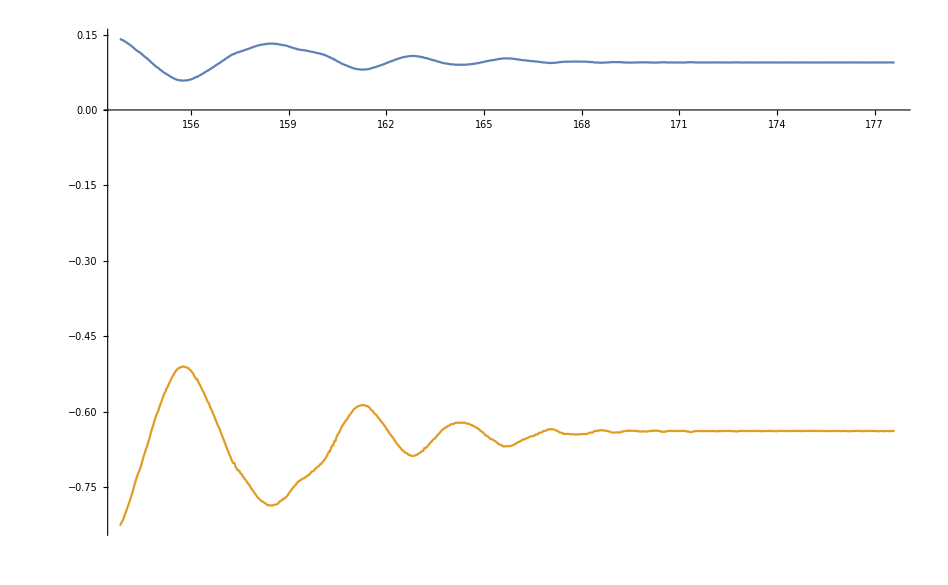

```mathematica
ListLinePlot[Transpose@{data[[All,1]],#}&/@Transpose[data][[2;;All]]]
```

# Process all the files

```mathematica
filenames=FileNames["data/raw/*.tsv"]
```

{data/raw/death1.tsv,data/raw/death2.tsv,data/raw/death3.tsv,data/raw/rocking1.tsv,data/raw/stabilizing1.tsv,data/raw/stablestart1.tsv}

```mathematica
Do[data=preprocess[Import[f]];Export[StringReplace[f,"/raw/"->"/cleaned/"],data],{f,filenames}]
```